### Reading files and building the grid/derivatives

Let’s define the initial number step, the final one, and the interval between each step that is going to be imported.
Foldername contains the location of the output file in your laptop.
For TypeOfFile, you can choose “constrained”, “bulk”, “boundary” or “gauge” depending which kind of file you want to read (and which one you have in the folder!).

```mathematica
FolderName="home/giulio/University/PhD/Simulations/NBB_gaussian_Lx60000_Ly10000_3d3iu10_6d6u010_Nx300_Ny50_u0d3_tzero50000_tau20000_A0d8_s0d5_dt0d219_rec_3";
TypeOfFile="constrained";

init=3148000; (*starts reading files from this timee step*)
end=3148000;   (*finish reading files at this timee step*)
each=1;                (*read n^th file, then n^th+each, then n^th+2 each, etc*)
FNames=Table[StringJoin[TypeOfFile<>"_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,init,end,each}];
Name1=Table[StringJoin["/"<>FolderName<>"/",
FNames[[i]],".h5"],{i,FNames//Length}];
dt=Import[Name1[[-1]],"Attributes"][[3,1]];
Timing[Obj=Module[{lastValid},Table[If[FileExistsQ[Name1[[i]]],lastValid=Import[Name1[[i]],"Data"];
lastValid,lastValid (*reuse previous if missing*)],{i,1,Length[Name1]}]];
(*Obj=Table[Import[Name1[[i]],"Data"](*[[1]]*),{i,1,Name1//Length}]*)];//AbsoluteTiming
Print["you have imported: "<>ToString[FNames//Length]<>" snapshot"];
(*"/home/giulio/University/PhD/JeccoGt2/examples/BB_QNM_1D_4p1_Vchannel_xpert/"*)
Print["defining times vector ..."]
times=Table[tim dt each+init dt,{tim,1,Obj//Length}];
(*snapshots=Table[(tim-1)  each+init ,{tim,1,Obj//Length}];*)
nt=times//Length;
Print["dt = "<>ToString[dt]]
Print["final time = "<>ToString[Import[Name1[[-1]],"Attributes"][[3,2]]//FullForm]]
```

{0.013866,Null}

you have imported: 1 snapshot

defining times vector ...

dt = 0.219

final time = 689412.0000102228`

#### Grid

```mathematica
(*you can just run this block, it define the grid directly from your h5 file*)
```

It’s usefull to have the XY grid explicitly in order to make more understandable plots.
Note! In the grid, the last point is not considered!!!
This because of the periodic boundary conditions.

```mathematica
ay=Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
by=-Abs[Import[Name1[[1]],"Attributes"][[5,3,1]]];
Ly=ay-by;
ax=Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
bx=-Abs[Import[Name1[[1]],"Attributes"][[5,3,2]]];
Lx=ax-bx;
NPoints=Obj[[1,1,;;]]//Length
```

50

```mathematica
Import[Name1[[1]],"Attributes"][[5,3]]
```

{-5000.,-30000.,3.3}

```mathematica
xValues=Range[bx,ax,(ax 2)/(Obj[[1,1,1,;;]]//Length)][[1;;-2]];
yValues=Range[by,ay,(ay 2)/(Obj[[1,1,;;]]//Length)][[1;;-2]];
nx=xValues//Length;
ny=yValues//Length;
dx=xValues[[2]]-xValues[[1]];
dy=yValues[[2]]-yValues[[1]];
```

```mathematica
nx
ny
```

300

50

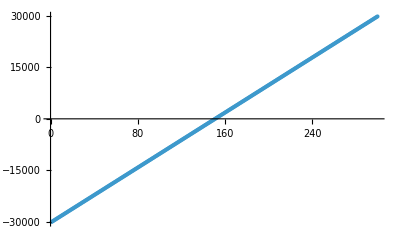

```mathematica
ListPlot[xValues]
```

The u grid is inserted ‘manually’, but I don’t use it  much in the analysis.

```mathematica
prec=20
uOuterMin=33/10;(*The boundary of the inner subdomain*)
uOuterMax= 66/10;(*The boundary of the last outer subdomain, should be close to the horizon*)
uOuterDomains=1;(*Number of outer subdomain*)
uOuterNodes=10;(*Number of points in each outer subdomains*)
uInnerNodes=10;(*Number of points in the inner subdomains*)
InterfaceNodes=Table[uOuterMin+i(uOuterMax-uOuterMin)/uOuterDomains,{i,0,uOuterDomains,1}];(*This gives the nodes where the subdomains meet*)
```

20

```mathematica
GetuDomain2[uOutMin_,uOutmax_,uOutDomains_,uOutNodes_,uInnNodes_,IntfaceNodes_]:=Module[{uu=uOutMin},
XInn=Table[-Cos[Pi i/(uInnNodes-1)],{i,0,uInnNodes-1}];
uInner=N[Table[(IntfaceNodes[[1]]+0)/2+(IntfaceNodes[[1]]-0)/2 XInn[[i]],{i,1,uInnNodes}],prec];
XOut=Table[-Cos[Pi i/(uOutNodes-1)],{i,0,uOutNodes-1}];
uOut=N[Table[Table[1/2(IntfaceNodes[[j]]+IntfaceNodes[[j-1]])+1/2(IntfaceNodes[[j]]-IntfaceNodes[[j-1]])XOut[[i]],{i,1,uOutNodes}],{j,2,IntfaceNodes//Length}],prec];
(*Print[Flatten[uOut,{1}]//Dimensions];*)
Insert[Flatten[uOut,{1}],uInner,1]
]
```

```mathematica
uValues=GetuDomain2[uOuterMin,uOuterMax,uOuterDomains,uOuterNodes,uInnerNodes,InterfaceNodes];
```

```mathematica
{uValues1,uValues2(*,uValues3,uValues4*)}=uValues;
```

#### Derivatives

```mathematica
(*you can just run this block, it define the derivatives directly from the grid*)
```

```mathematica
Clear[d];
d[1,0]=NDSolve`FiniteDifferenceDerivative[Derivative[1,0],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xValues,yValues},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
(*d[2,0]=NDSolve`FiniteDifferenceDerivative[Derivative[2,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,1]=NDSolve`FiniteDifferenceDerivative[Derivative[0,1],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,2]=NDSolve`FiniteDifferenceDerivative[Derivative[0,2],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[0,6]=NDSolve`FiniteDifferenceDerivative[Derivative[0,6],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];
d[6,0]=NDSolve`FiniteDifferenceDerivative[Derivative[6,0],{xgrid,ygrid},DifferenceOrder->{"Pseudospectral","Pseudospectral"},PeriodicInterpolation->{True,True}];*)
```

### Data Analysis

Here I visualise the fields and analysis different quantities of interest.
Obj is the variable that contains all your data.
The entries are: {time, field, y index, x index, u index}
Below I visualise the keys, they show the fields Obj contains. c=n corresponds to the n subdomain of u.

```mathematica
Obj[[-1]]//Keys
```

{/data/3148000/fields/Sd c=2,/data/3148000/fields/S c=2,/data/3148000/fields/A c=2,/data/3148000/fields/Fx c=2,/data/3148000/fields/Fx c=1,/data/3148000/fields/Fy c=1,/data/3148000/fields/Sd c=1,/data/3148000/fields/Gd c=2,/data/3148000/fields/Gd c=1,/data/3148000/fields/Bd c=1,/data/3148000/fields/Bd c=2,/data/3148000/fields/Fy c=2,/data/3148000/fields/A c=1,/data/3148000/fields/S c=1}

I use the values of Fy, Fx and A at the boundary. In my case this correspond to the index 6, 5 and -2 (they vary depending on which type of quantity you are analysing, and on the number of u-subdomains).
For getting the velocities, I am using the expression coming from  https://arxiv.org/abs/1912.00032.

```mathematica
ClearAll[ss]
fy=Table[Obj[[ss,6,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
fx=Table[Obj[[ss,5,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
a3=Table[Obj[[ss,-2,j,i,1]],{ss,1,nt},{i,1,xValues//Length
},{j,1,yValues//Length}];
u0=(-a3)^(1/2);
ux=Table[(fx[[tt]]-d[1,0][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}](*-fx u0*);
uy=Table[(fy[[tt]]-d[0,1][a3[[tt]]])/a3[[tt]],{tt,1,a3//Length}](*-fy u0*);
```

Here I compute and plot the vorticity

```mathematica
VorticityTranslated=Join[((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,150;;]],((d[1,0][uy[[ss]]]-d[0,1][ux[[ss]]])//Transpose)[[;;,;;149]],2];
VorticityToPlot=Flatten[Table[{xValues[[i]],yValues[[j]],VorticityTranslated[[j,i]]},{i,1,nx},{j,1,ny}],1];
```

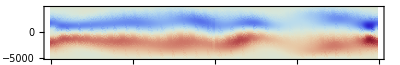

```mathematica
ListDensityPlot[VorticityToPlot,PlotRange->{All,All}, PlotLegends->True,
PlotLabel->"vorticity t="<>ToString[(ss-1) dt each+init dt],ImageSize->Full,AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]]),ColorFunction->"ThermometerColors"]
```

Here I plot the velocity vector field.

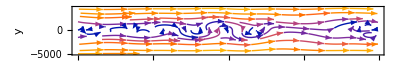

```mathematica
t=(ux//Length);
a=1;
b=ux[[1]]//Length;
c=1;
dd=uy[[1,1]]//Length;
midpoint=(ux[[1]]//Length)/2//Floor;
Show[Join[Table[{{xValues[[i+1]],yValues[[j]]},{ux[[t,i+midpoint,j]],uy[[t,i+midpoint,j]]}},{i,0,midpoint
},{j,c,dd}],Table[{{xValues[[i+midpoint]],yValues[[j]]},{ux[[t,i+1,j]],uy[[t,i+1,j]]}},{i,0,midpoint
},{j,c,dd}]]//
ListStreamPlot[#,(*PlotRange->{{-200,200},{-200,200}},*)PlotLegends->Automatic,ImageSize->Full,StreamPoints->Fine,PlotLabel->"t="<>ToString[t dt each+init dt](*,10->10[0.01]*),StreamStyle->{Arrowheads[0.007],Thick[0.05]},AspectRatio->(yValues[[dd]]-yValues[[c]])/(xValues[[b]]-xValues[[a]])(*,StreamPoints->50000*),LabelStyle->Directive[FontSize->16],(*axes labels,ticks,etc.*)BaseStyle->{FontSize->16},FrameLabel->{"x","y"}]&(*,ParametricPlot[ellipse[θ,(0.5 Ly)/(2Pi),(0.5 Ly)/(2Pi)],{θ,0,2Pi}]*)]
```